```mathematica
rearrange[f_,k_,S_,n0_:1]:=Module[{i=1,j=1,partial=0,rearg={},seq,pos,neg},
seq=Table[f,{n,n0,k+n0-1}];
pos=MapThread[{#1,#2}&,{Flatten[Position[seq,_?(#>0&),1]],Select[seq,#>0&]}];
neg=MapThread[{#1,#2}&,{Flatten[Position[seq,_?(#<0&),1]],Select[seq,#<0&]}];
While[i<=Length[pos]&& j<=Length[neg],
If[partial<S,partial+=pos[[i,2]];AppendTo[rearg,{pos[[i,1]],pos[[i,2]],N[partial,10]}];i+=1;];
If[partial≥S,partial+=neg[[j,2]];AppendTo[rearg,{pos[[j,1]]+1,pos[[j,2]],N[partial,10]}];j+=1;];
];
rearg
]
```

```mathematica
plotData[f_,k_,S_,n0_:1]:=Show[ListLinePlot[rearrange[f,k,S,n0][[All,3]],PlotStyle->{Red,Thickness[0.0025]},AxesLabel->{"n","Částečné součty"},PlotLabel->HoldForm[Sum[f,{n,n0,Infinity}]]],Plot[S,{x,1,k},PlotStyle->{Black, Dashed}]]
```

```mathematica
k=100;S=1;f=(-1)^(n-1)/n;
```

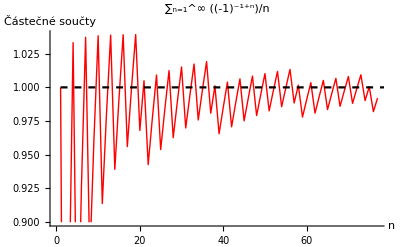

```mathematica
fig=plotData[f,k,S]
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Export["serie1_1.png",fig,"PNG",ImageResolution->200];
```

```mathematica
k=500;S=2;
```

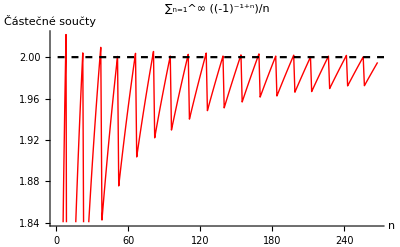

```mathematica
fig=plotData[f,k,S]
```

```mathematica
Export["serie1_2.png",fig,"PNG",ImageResolution->200];
```

```mathematica
S=-0.5;
```

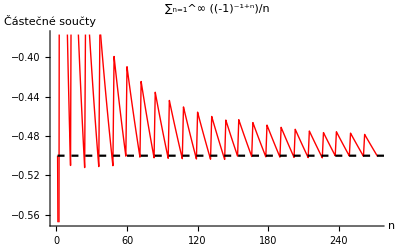

```mathematica
fig=plotData[f,k,S]
```

```mathematica
Export["serie1_3.png",fig,"PNG",ImageResolution->200];
```

```mathematica
k=100;S=0.5;n0=2;f=(-1)^n/(n*Log[n]);
```

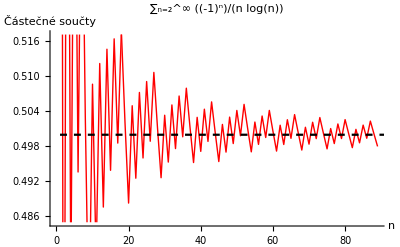

```mathematica
fig=plotData[f,k,S,n0]
```

```mathematica
Export["serie2_1.png",fig,"PNG",ImageResolution->200];
```

```mathematica
S=1;
```

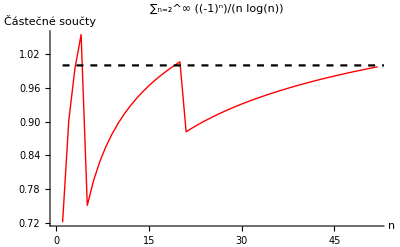

```mathematica
fig=plotData[f,k,S,n0]
```

```mathematica
Export["serie2_2.png",fig,"PNG",ImageResolution->200];
```

```mathematica
k=100;S=1;f=Sin[n]/n;
```

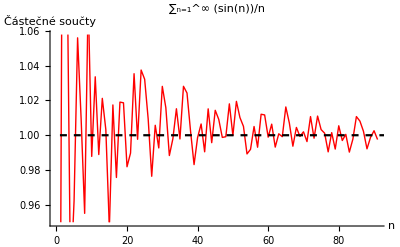

```mathematica
fig=plotData[f,k,S]
```

```mathematica
Export["serie3_1.png",fig,"PNG",ImageResolution->200];
```

```mathematica
k=1000;S=3;
```

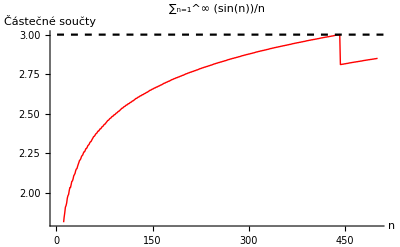

```mathematica
fig=plotData[f,k,S]
```

```mathematica
Export["serie3_2.png",fig,"PNG",ImageResolution->200];
```